```mathematica
(* coefficients *)
μ=1;
K0=-1;
dk=0.9;
```

```mathematica
(* vector field *)
vec1[A_,B_]:=B;
vec2[A_,B_]:=-(1/(4*dk))*(μ*A+c*B+K0*A^3);
```

```mathematica
(* equilibria *)
T={0,0};
R={1,0};
```

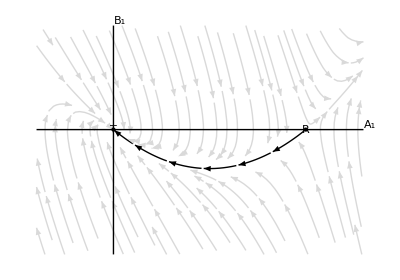

```mathematica
(* stream plot : supercritical front *)
c=4;
xmin=-0.4;
xmax=1.3;
ymin=-0.3;
ymax=0.25;
linex=Line[{{xmin,0},{xmax,0}}];
liney=Line[{{0,ymin},{0,ymax}}];
vecfield=StreamPlot[{vec1[x,y],vec2[x,y]},{x,xmin,xmax},{y,ymin,ymax},
Epilog->{Black,PointSize[Large],Point[{T,R}],Text[Style[" T ",Italic,Larger],T,{1,-2},Background->White],
Text[Style[" R ",Italic,Larger],R,{1,-2},Background->White],
Text[Style["A_1",Italic,Larger],{xmax,0},{-1.3,-1.5}],
Text[Style["B_1",Italic,Larger],{0,ymax},{-1.5,-1}],
linex,liney},
StreamColorFunction->None,
StreamStyle->LightGray,
StreamScale->0.1,
StreamPoints->{{{R-0.005*{(1+√3),1},Black},
			Automatic}},
FrameTicks->True,
Frame->None,
AspectRatio->0.7
]
```

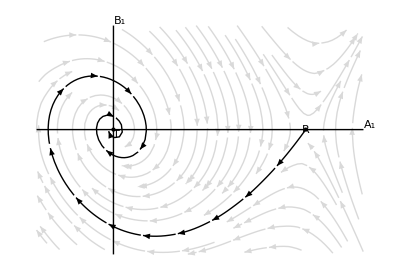

```mathematica
(* stream plot : supercritical front *)
c=0.8;
xmin=-0.4;
xmax=1.3;
ymin=-0.3;
ymax=0.25;
linex=Line[{{xmin,0},{xmax,0}}];
liney=Line[{{0,ymin},{0,ymax}}];
vecfield=StreamPlot[{vec1[x,y],vec2[x,y]},{x,xmin,xmax},{y,ymin,ymax},
Epilog->{Black,PointSize[Large],Point[{T,R}],Text[Style["T",Italic,Larger],T,{-3.1,1.5},Background->White],
Text[Style[" R ",Italic,Larger],R,{1,-2},Background->White],
Text[Style["A_1",Italic,Larger],{xmax,0},{-1.3,-1.5}],
Text[Style["B_1",Italic,Larger],{0,ymax},{-1.5,-1}],
linex,liney},
StreamColorFunction->None,
StreamStyle->LightGray,
StreamScale->0.1,
StreamPoints->{{{R-0.015*{0.8501702878357026,0.5265078173031799},Black},
			Automatic}},
FrameTicks->True,
Frame->None,
AspectRatio->0.7
]
```

```mathematica
Eigenvectors[{{0,1},{-1/(4*dk)*(μ+3*K0*R[[1]]),-c/(4*dk)}}]
```

{{-0.744376,0.667761},{0.85017,0.526508}}